```mathematica
e=500;
```

```mathematica
z=950;
```

```mathematica
t[d_]:=(A[d]-e)/(d)
```

```mathematica
r[d_]:=(z-A[d])/(30.1-d)
```

```mathematica
y[A_]:=Piecewise[{{t[d]-1, r[d]< t[d]-1}, {t[d]+2, r[d]>t[d]+2}, {r[d], True}}]
```

```mathematica
s=NDSolve[{A'[d]==y[A[d]],A[1]==e+(z-e)/30+5},A, {d,1,30}][[1,1]]
```

A→InterpolatingFunction[{{1.,30.}},<>]

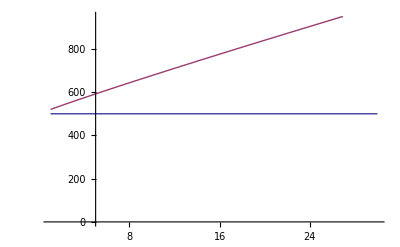

```mathematica
Plot[{e,Evaluate[A[d]/.s]},{d,1,30},PlotRange->{0,z}]
```

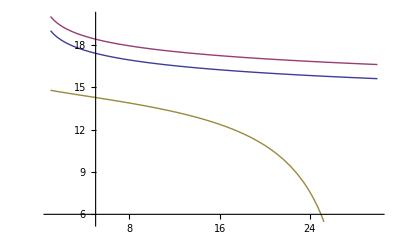

```mathematica
Plot[{Evaluate[y[d]/.s],Evaluate[t[d]/.s],Evaluate[r[d]/.s],},{d,1,30}]
```

```mathematica
Evaluate[A[d]/.s]/.d->30
```

997.964